```mathematica
SetDirectory[NotebookDirectory[]];
```

## Criminal Acts in Montreal, Quebec, Canada

Dataset contains criminal activities registered by SPVM.

https://donnees.montreal.ca/ville-de-montreal/actes-criminels

Let’s get the data:

```mathematica
data =Import["https://data.montreal.ca/dataset/5829b5b0-ea6f-476f-be94-bc2b8797769a/resource/c6f482bf-bf0f-4960-8b2f-9982c211addd/download/interventionscitoyendo.csv"];
```

Let’s see dimensions of the data:

```mathematica
data // Dimensions
```

{204997,8}

```mathematica
headers =First @ data
```

{CATEGORIE,DATE,QUART,PDQ,X,Y,LONGITUDE,LATITUDE}

Let’s generate Dataset to make it easier to work with data.

```mathematica
ds = Dataset[AssociationThread[headers -> #] & /@ Rest[data]];
```

Let’s enrich this Dataset.

```mathematica
mtlCenter = GeoPosition[{45.5035457,-73.6685297}];
```

```mathematica
eds = ds[All,<|#,
"OccurenceDate"-> FromDateString[#DATE],
"Day"->DayName[FromDateString[#DATE]],
 "Position" -> GeoPosition[{#LATITUDE, #LONGITUDE}],
"DistanceFromCenter" -> GeoDistance[mtlCenter,GeoPosition[{#LATITUDE, #LONGITUDE}]]|>&];
```

```mathematica
eds[1,All]
```

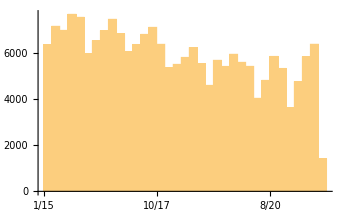

```mathematica
DateHistogram[FromDateString /@ ds[All,"DATE"]]
```

What is the day of the week that has the most crime?

```mathematica
ReverseSortBy[Tally[eds[All, "Day"]], Rest]
```

Where on the map do crimes happen?

```mathematica
ReverseSort[GroupBy[ds,"CATEGORIE"][All,Length]]
```

```mathematica
ds;
```

```mathematica
mtl = GeoPosition[{45.5581968,-73.870384}];
```

```mathematica
distnacedFromMtl ={GeoDistance[mtl, #, UnitSystem->"Metric"], #} & /@ positions;
```

```mathematica
withinMontreal =Select[distnacedFromMtl, #[[1]] < Quantity[100,"Kilometers"]&];
```

Select::normal: Nonatomic expression expected at position 1 in Select[positions,#1⟦1⟧<100&].

```mathematica
GeoHistogram[eds[Select[#OccurenceDate < DateObject[{2021,1,1}] && #DistanceFromCenter < Quantity[50, "Kilometers"]&]][All, "Position"]]
```

-Graphics-

```mathematica
First@eds
```

## Wrangle data

```mathematica
cleanData[data_] :=data[Select[#DistanceFromCenter < Quantity[50, "Kilometers"]&]];
```

```mathematica
clnData = cleanData[eds];
```

```mathematica
clnData
```

Dataset[<>]

## Visualize crimes in MTL

## Point classes

We want to have three types of points,  fresh -> mid -> old (yellow) -> deleted (none). On second thought, having different colors for points does not make sense since it’ll confuse the viewer as to the value of those. It’s better only to use one color and display those in a window (moving window).

```mathematica
getDataInWindow[data_, start_, end_] := data[Select[(start <#OccurenceDate) &&  (#OccurenceDate < end) &]];
```

If you would want to play with decay function:

Depending on how far the point is from current date then set it’s opacity

```mathematica
decay[data_, currentDate_] := {PointSize[Large], Red, Opacity[0.2], Point[#]}& /@ data;
```

```mathematica
dates =Table[{DateObject[d], (DateObject[d] + Quantity[3,"Months"]) },{d,  DateRange[{2014,12,1},{2016,2, 1}, Quantity[3, "Months"]]}]
```

{{Mon 1 Dec 2014 00:00:00GMT-5,Sun 1 Mar 2015 00:00:00GMT-5},{Sun 1 Mar 2015 00:00:00GMT-5,Mon 1 Jun 2015 00:00:00GMT-5},{Mon 1 Jun 2015 00:00:00GMT-5,Tue 1 Sep 2015 00:00:00GMT-5},{Tue 1 Sep 2015 00:00:00GMT-5,Tue 1 Dec 2015 00:00:00GMT-5},{Tue 1 Dec 2015 00:00:00GMT-5,Tue 1 Mar 2016 00:00:00GMT-5}}

```mathematica
d = dates[[3]]
```

{Mon 1 Jun 2015 00:00:00GMT-5,Tue 1 Sep 2015 00:00:00GMT-5}

```mathematica
d[[1]]<d[[2]]
```

True

```mathematica
getDataInWindow[clnData, d[[1]], d[[2]]]
```

Failure[…]

```mathematica
toPoints[data_] := data[All, "Position", {PointSize[Large], Red, Point[#]}&];
```

Working around a bug.

```mathematica
dateL = Table[DayRound @DateObject[d],{d,DateRange[{2014,12,1,0,0,0},{2016,2,1,0,0,0}, Quantity[3, "Months"]]}]
```

{Mon 1 Dec 2014,Sun 1 Mar 2015,Mon 1 Jun 2015,Tue 1 Sep 2015,Tue 1 Dec 2015}

```mathematica
dateR = Table[DayRound @DateObject[d],{d,DateRange[{2015,2,1,0,0,0},{2016,2,1,0,0,0}, Quantity[3, "Months"]]}]
```

{Sun 1 Feb 2015,Fri 1 May 2015,Sat 1 Aug 2015,Sun 1 Nov 2015,Mon 1 Feb 2016}

```mathematica
combined =Table[d, {d,MapThread[{#1, #2}&, {dateL, dateR}]}]
```

{{Mon 1 Dec 2014,Sun 1 Feb 2015},{Sun 1 Mar 2015,Fri 1 May 2015},{Mon 1 Jun 2015,Sat 1 Aug 2015},{Tue 1 Sep 2015,Sun 1 Nov 2015},{Tue 1 Dec 2015,Mon 1 Feb 2016}}

```mathematica
ParallelTable[Export[StringJoin["data_viz/",DateString[d[[1]],"ISODate"], ".png"],
GeoGraphics[ toPoints[getDataInWindow[
clnData, 
d[[1]], 
d[[2]]]],
GeoRange->Quantity[25,"Kilometers"], 
GeoCenter->mtlCenter,
GeoZoomLevel->13,
PlotLabel->Style[
"MTL crime " <> DateString[d[[1]]] <> "-" <> DateString[d[[2]]],
"Subtitle"], (*TODO: Make the plot label bigger and move at the bottom of the image*)
ImageSize->Full]],
{d,  combined}]
```